## Make some graphs

### Oscillation length in matter and vacuum

parameters in units of GeV^(n)

```mathematica
deltam2=10^(-4)*10^(-18)(*GeV^2*)
gF=1.17*10^(-5) (*GeV^(-2)*)
```

1/10000000000000000000000

0.0000117

Energy is in units of MeV, length is meter.

```mathematica
lengthV[energy_]=4Pi (energy*1000)/deltam2*1.24*10^(-15)
```

1.55823×10^8 energy

ne is in units of m^-3

```mathematica
lengthM[ne_]=1.24*10^(-15)*2/(√2 gF ne*5*10^(32))
```

(2.99765×10^-43)/ne

```mathematica
eqSol=Solve[lengthV[energy]==lengthM[ne],energy]
```

{{energy→(1.92375×10^-51)/ne}}

Define the line where the two lengths are equal

```mathematica
eqEnergy[ne_]=energy/.eqSol[[1]]
```

(1.92375×10^-51)/ne

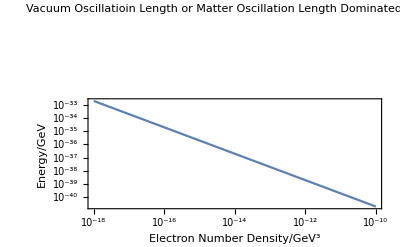

```mathematica
LogLogPlot[eqEnergy[ne],{ne,10^(-18),10^(-10)},Frame->True,PlotRange->{{10^(-18),10^(-10)},{eqEnergy[10^(-18)],eqEnergy[10^(-10)]}},GridLines->{{{10^(-15),Directive[Black,Thick]}},None},PlotLabel->"Vacuum Oscillatioin Length or Matter Oscillation Length Dominated Region",ImageSize->Full,FrameLabel->{"Electron Number Density/GeV^3","Energy/GeV"},Epilog->{Style[Text["Matter Characteristic Length Larger",Log@{10^(-16),10^(-5)5}],14],Style[Text["Vacuum Oscillation Length Larger",Log@{10^(-12),10^(-2)5}],14]}]
```

```mathematica
LogLogPlot[eqEnergy[ne],{ne,10^(-18),10^(-10)},Frame->True,PlotRange->{{10^(-18),10^(-10)},{eqEnergy[10^(-18)],eqEnergy[10^(-10)]}},GridLines->{{{3*10^(-16),Directive[Blue,Thick,Dashed]},{3.6*10^(-15),Directive[Red,Thick,Dashed]},{10^(-14),Directive[Green,Thick,Dashed]}},None},Filling->{1->Top,1->Bottom},FillingStyle->{Directive[Opacity[0.7],LightBlue],Directive[Opacity[0.7],LightOrange]},PlotLabel->"Vacuum Oscillatioin Length or Matter Oscillation Length Dominated Region",ImageSize->Full,FrameLabel->{"Electron Number Density/GeV^3","Energy/GeV"},Epilog->{Style[Text["Matter Characteristic Length Larger",Log@{10^(-16),10^(-5)5}],14],Style[Text["Vacuum Oscillation Length Larger",Log@{10^(-12),10^(-2)5}],14]},PlotLegends->Placed[LineLegend[{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Green,Dashed]},{"Water","Earth Core","Solar Core"}],{Center,Above}]]
```

-Graphics-

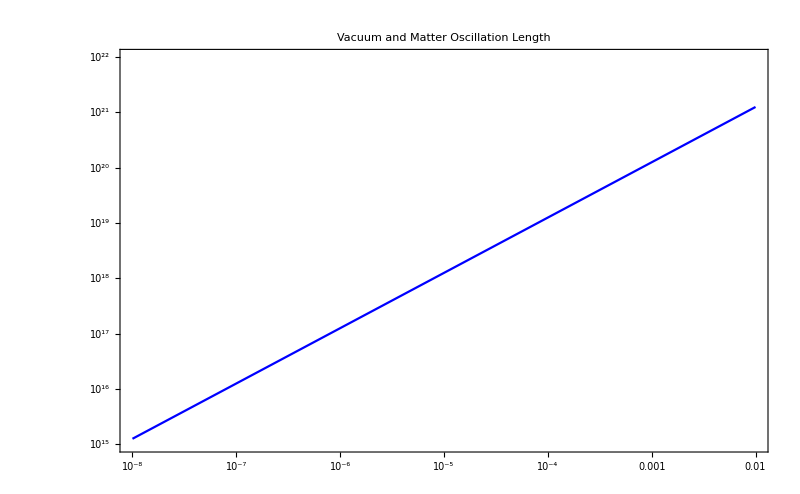

```mathematica
vacLenPlt=LogLogPlot[lengthV[energy],{energy,10^(-8),10^(-2)},PlotRange->{{10^(-8),10^(-2)},{10^(15),10^(22)}},PlotStyle->Blue,ImagePadding->25,Frame->{True,True,False,True},FrameStyle->{Blue,Automatic,Automatic,Automatic},ImageSize->800,FrameTicks->{All,All,None,All},PlotLabel->"Vacuum and Matter Oscillation Length"]
```

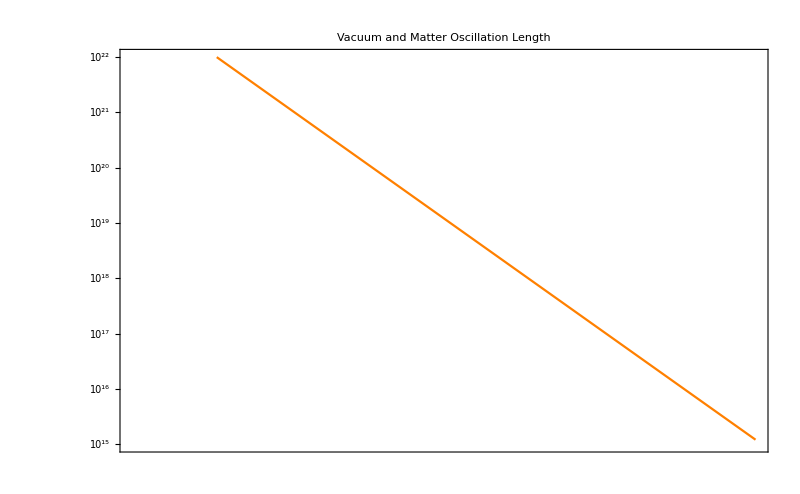

```mathematica
matLenPlt=LogLogPlot[lengthM[ne],{ne,10^(-18),10^(-10)},PlotRange->{{10^(-18),10^(-10)},{10^(15),10^(22)}},PlotStyle->Orange,ImagePadding->25,Frame->{False,True,True,True},FrameTicks->{None,All,All,All},FrameStyle->{Automatic,Automatic,Orange,Automatic},ImageSize->800,PlotLabel->"Vacuum and Matter Oscillation Length"]
```

```mathematica
lenPlt=Overlay[{vacLenPlt,matLenPlt}]
```

-Graphics--Graphics-

```mathematica
Export["../assets/lengthComparison.png",lenPlt]
```

../assets/lengthComparison.png